```mathematica
Integrate[  u Sin[ omega ( t - Sqrt[y^2 + u^2]/c )]/Sqrt[ y^2 + u^2], u]
```

(c Cos[omega t] Cos[(omega √(u^2+y^2))/c])/omega+(c Sin[omega t] Sin[(omega √(u^2+y^2))/c])/omega

```mathematica
Integrate[  u Sin[ omega ( t - Sqrt[y^2 + u^2]/c )]/Sqrt[ y^2 + u^2], {u, 0, Sqrt[c^2 t^2 - y^2]}]
```

ConditionalExpression[(c (Cos[omega (t-(√(c^2 t^2))/c)]-Cos[omega (t-(√(y^2))/c)]))/omega,y/(√(c^2 t^2-y^2))∈Reals||Re[y/(√(c^2 t^2-y^2))]≠0||Im[y/(√(c^2 t^2-y^2))]≥1||Im[y/(√(c^2 t^2-y^2))]≤-1]

```mathematica
Simplify[ Cos[t]Cos[y] + Sin[t]Sin[y]]
```

Cos[t-y]

```mathematica
TrigReduce[ 1- Cos[t]Cos[y] + Sin[t]Sin[y]]
```

1-Cos[t+y]

```mathematica
TrigReduce[Sin[x]^2]
```

1/2 (1-Cos[2 x])

```mathematica
Integrate[ Sin[omega t]^2, {t, 0, 2 Pi/omega}]
```

π/omega

```mathematica
Plot3D[ Sin[t - Sqrt[y^2]], {t, 0, 10}, {y, -10, 10}, AxesLabel -> {t, y, sin(t - Abs[y])}]
```

-Graphics3D-

```mathematica
Plot[ {Sin[x], Sin[x-1], Sin[x-2]}, {x, 0, 3 Pi}]
```

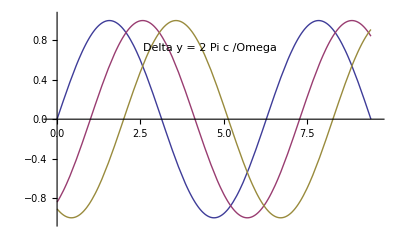

Set::write: Tag Times in Delta\ y is Protected.